# Anharmonic Chains

Reference: H. Spohn, Nonlinear fluctuating hydrodynamics for anharmonic chains. J. Stat. Phys. 154, 1191-1227 (2014)

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Framework: Inverse CDF for shoulder potential

```mathematica
(* "shoulder" potential *)
Subscript[V, val][x_]:=If[x<c,∞,If[x<d,h,0]]
```

```mathematica
(*Subscript[c, val]=2/3;
Subscript[d, val]=9/7;
Subscript[h, val]=5/4;*)
```

```mathematica
Subscript[c, val]=1/2;
Subscript[d, val]=1;
Subscript[h, val]=1;
```

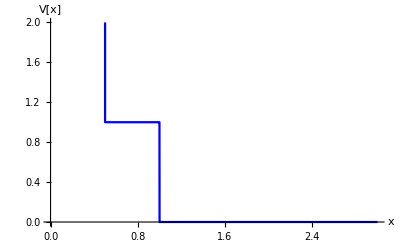

```mathematica
Plot[Subscript[V, val][x]/.{c->Subscript[c, val],d->Subscript[d, val],h->Subscript[h, val]}/.{∞->1000},{x,0,3},AxesLabel->{"x","V[x]"},PlotStyle->Blue,AxesOrigin->{0,0},PlotRange->{Automatic,{0,2}}]
```

```mathematica
(* spatial part of the partition function *)
Zspatial[p_,β_,{c_,d_,h_}]:=Module[{q=p β},1/q ⅇ^(-d q)(1+ⅇ^(-h β)(ⅇ^((d-c)q)-1))]
```

```mathematica
InvCDFshoulder1[p_,β_,t_,{c_,d_,h_}]:=Module[{q=p β,zt=Zspatial[p,β,{c,d,h}]t},c-1/q Log[1-ⅇ^(c q+h β) q zt]]
```

```mathematica
InvCDFshoulder2[p_,β_,t_,{c_,d_,h_}]:=Module[{q=p β},d-1/q(Log[1+ⅇ^(-h β)(ⅇ^((d-c)q)-1)]+Log[1-t])]
```

```mathematica
DiscontinuityPosition[p_,β_,{c_,d_,h_}]:=Module[{q=p β},(1+1/(ⅇ^(-h β)(ⅇ^((d-c)q)-1)))^-1]
```

```mathematica
InvCDFshoulder[p_,β_,t_,{c_,d_,h_}]:=If[t<DiscontinuityPosition[p,β,{c,d,h}],InvCDFshoulder1[p,β,t,{c,d,h}],InvCDFshoulder2[p,β,t,{c,d,h}]]
```

## Example data

```mathematica
(* pressure *)
Subscript[p, val]=6/5;
N[%]
```

1.2

```mathematica
(* inverse temperature *)
Subscript[β, val]=2;
```

```mathematica
(* check: values agree at C^1 discontinuity position*)
DiscontinuityPosition[Subscript[p, val],Subscript[β, val],{c,d,h}];
FullSimplify[InvCDFshoulder1[Subscript[p, val],Subscript[β, val],%,{c,d,h}]-InvCDFshoulder2[Subscript[p, val],Subscript[β, val],%,{c,d,h}],Assumptions:>{0<c,c<d,h>0}]/.{d->1.3,c->0.75,h->1.2}
```

3.46945×10^-17

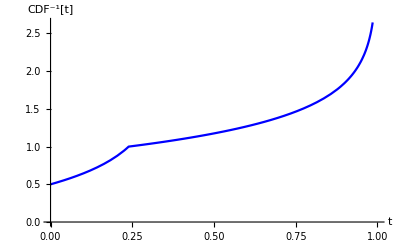

```mathematica
(* plot inverse function *)
Plot[InvCDFshoulder[Subscript[p, val],Subscript[β, val],t,{Subscript[c, val],Subscript[d, val],Subscript[h, val]}],{t,0,1},PlotStyle->Blue,AxesLabel->{"t","CDF^-1[t]"},AxesOrigin->{0,0}]
```

```mathematica
Subscript[icdf, dat]=Import["ensemble_test.dat","Real64"]
```

{0.5,0.551834,0.611044,0.680084,0.762881,0.866317,1.00057,1.0231,1.04691,1.07217,1.09906,1.12781,1.15869,1.19204,1.2283,1.26801,1.31191,1.36098,1.41662,1.48085,1.55682,1.6498,1.76966,1.93861,2.22742}

```mathematica
(* reference data *)
Subscript[icdf, dat,ref]=Table[FullSimplify[InvCDFshoulder[Subscript[p, val],Subscript[β, val],t,{Subscript[c, val],Subscript[d, val],Subscript[h, val]}]],{t,0,1-1/25,1/25}];
```

```mathematica
Export["ensemble_test_ref.dat",N[Subscript[icdf, dat,ref]],"Real64"];
```

```mathematica
(* example *)
Subscript[icdf, dat,ref]⟦{1,2,-1}⟧
```

{1/2,1+(5 Log[5])/6-5/12 Log[1+24 ⅇ^(6/5)-ⅇ^2],1+5/12 (2+Log[25]-Log[-1+ⅇ^(6/5)+ⅇ^2])}

```mathematica
(* compare (should be equal) *)
Norm[Subscript[icdf, dat]-Subscript[icdf, dat,ref]]
```

1.18948×10^-15